# 空间几何

```mathematica
irisData=ExampleData[{"MachineLearning","FisherIris"},"Data"];
{sepalLength,sepalWidth,petalLength,petalWidth}=Table[irisData[[i,1,j]],{j,1,4},{i,1,150}];
```

中垂线

```mathematica
dataset=Transpose@{sepalLength,sepalWidth};
cl=ClusterClassify[dataset,3]; (*3均值聚类*)
centroids=Mean@Pick[dataset,cl[dataset],#]&/@{1,2,3} (*计算数据的簇质心*)
```

{{5.75962,2.64615},{6.75918,3.1},{5.01633,3.45102}}

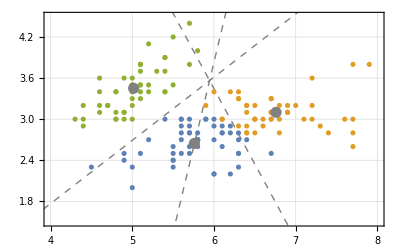

```mathematica
Show[
ListPlot[Pick[dataset,cl[dataset],#]&/@{1,2,3},PlotRange->{{4,8},{1.5,4.5}},PlotTheme->"Detailed"],(*k均值聚类结果*)
Graphics[{Gray,PointSize[0.02],Point[centroids]}],(*绘制簇质心*)
Graphics[{Gray,Dashed,PerpendicularBisector/@Subsets[centroids,{2}]}] (*两两簇质心的中垂线*)
]
```

旋转椭圆

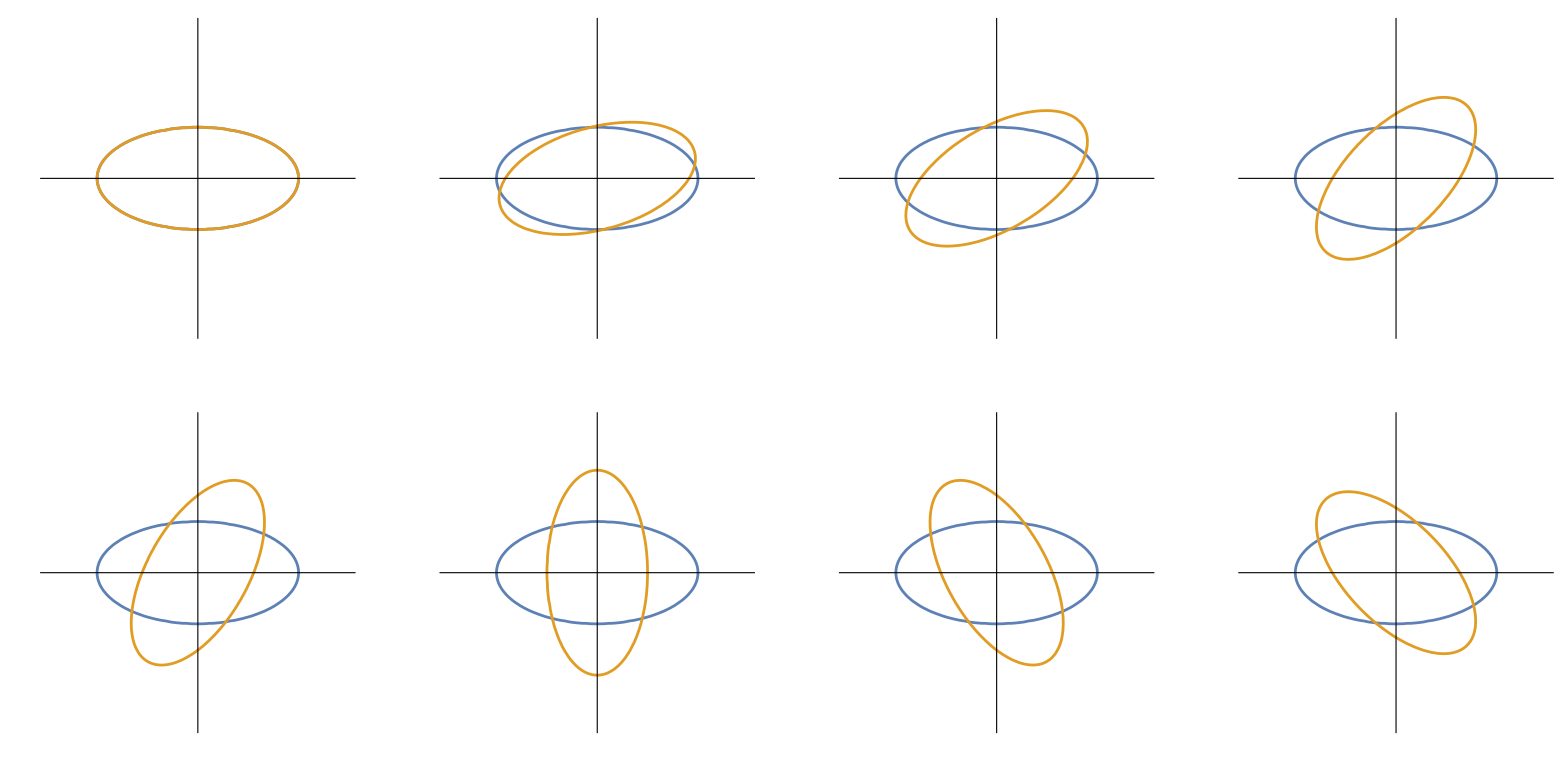

```mathematica
ContourPlot[{0.25 x1^2+x2^2==1(*基准椭圆*),{x1,x2}.RotationMatrix[#].{{0.25,0},{0,1}}.(Transpose@RotationMatrix[#]).{x1,x2}-1==0(*使用旋转矩阵实现旋转*)},{x1,-3,3},{x2,-3,3},PlotTheme->"Minimal"]&/@{0,Pi/12,Pi/6,Pi/4,Pi/3,Pi/2,2Pi/3,3Pi/4}//ArrayReshape[#,{2,4}]&//GraphicsGrid
```

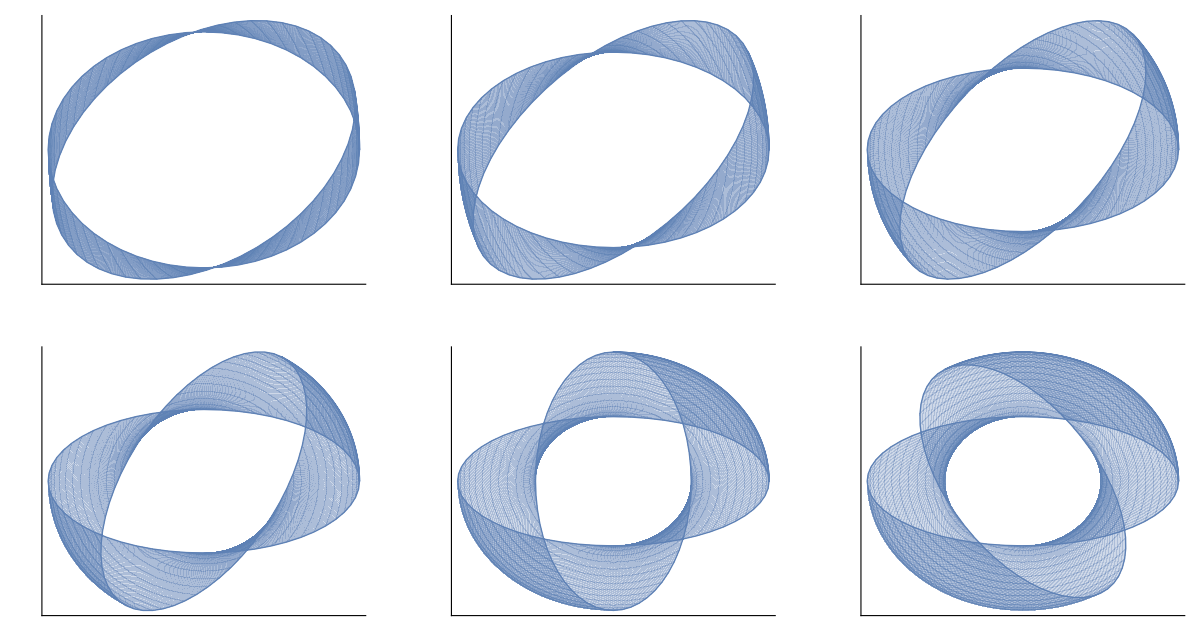

```mathematica
ParametricPlot[Evaluate@RotationTransform[θ][{2 Cos[u],Sin[u]}],{u,0,2Pi},{θ,0,#},PlotTheme->"Minimal"]&/@{Pi/12,Pi/6,Pi/4,Pi/3,Pi/2,2Pi/3}//ArrayReshape[#,{2,3}]&//GraphicsGrid
```

多元高斯分布

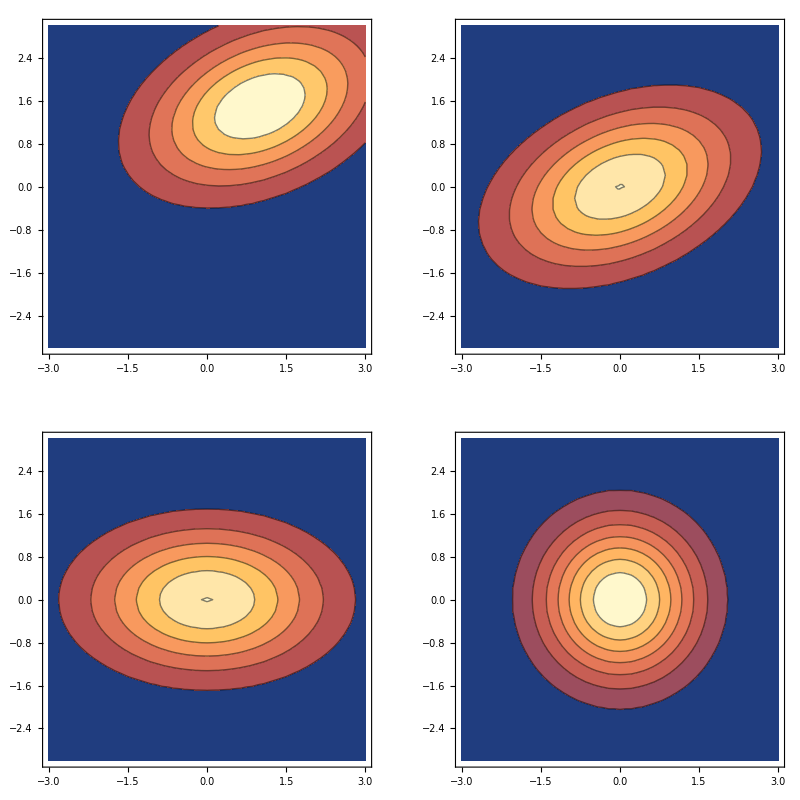

```mathematica
ContourPlot[PDF[MultinormalDistribution[#[[1]],#[[2]]],{x,y}],{x,-3,3},{y,-3,3},ImageSize->Small]&/@
{{{1,1.5},#}(*均值与协方差矩阵*),
{{0,0},#}(*中心化*),
{{0,0},DiagonalMatrix@Eigenvalues[#]}(*旋转*),
{{0,0},IdentityMatrix[2]}(*缩放*)
}&@{{2,1/2},{1/2,1}}(*协方差矩阵*)//ArrayReshape[#,{2,2}]&//GraphicsGrid
```

马氏距离

```mathematica
euDistance[x1_,x2_]:=EuclideanDistance[{x1,x2},Mean/@{sepalLength,petalLength}]
```

```mathematica
maDistance[x1_,x2_]:=Module[{mean,cov},
mean=Mean/@{sepalLength,petalLength};
cov=Covariance[Transpose@{sepalLength,petalLength}];
Sqrt[({x1,x2}-mean).Inverse@cov.({x1,x2}-mean)]
]
```

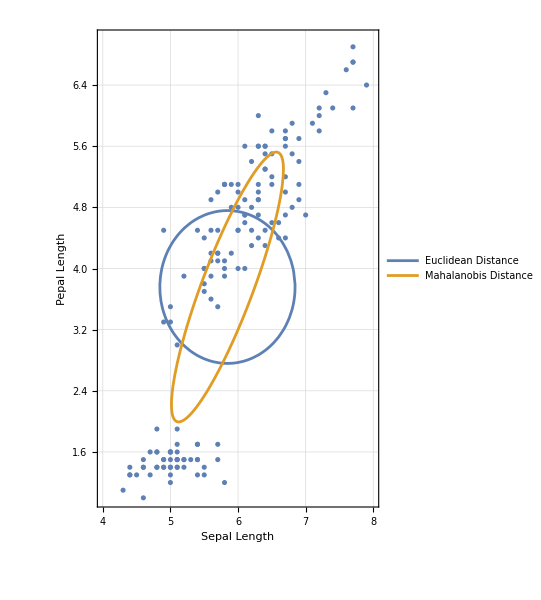

```mathematica
Show[ListPlot[Transpose@{sepalLength,petalLength},PlotTheme->"Detailed",FrameLabel->{"Sepal Length","Pepal Length"},PlotRange->{{4,8},{1,7}},AspectRatio->3/2],ContourPlot[{euDistance[x1,x2]==1,maDistance[x1,x2]==1},{x1,4,8},{x2,1,7},AspectRatio->3/2,PlotLegends->{"Euclidean Distance","Mahalanobis Distance"}]]
```

旋转双曲线

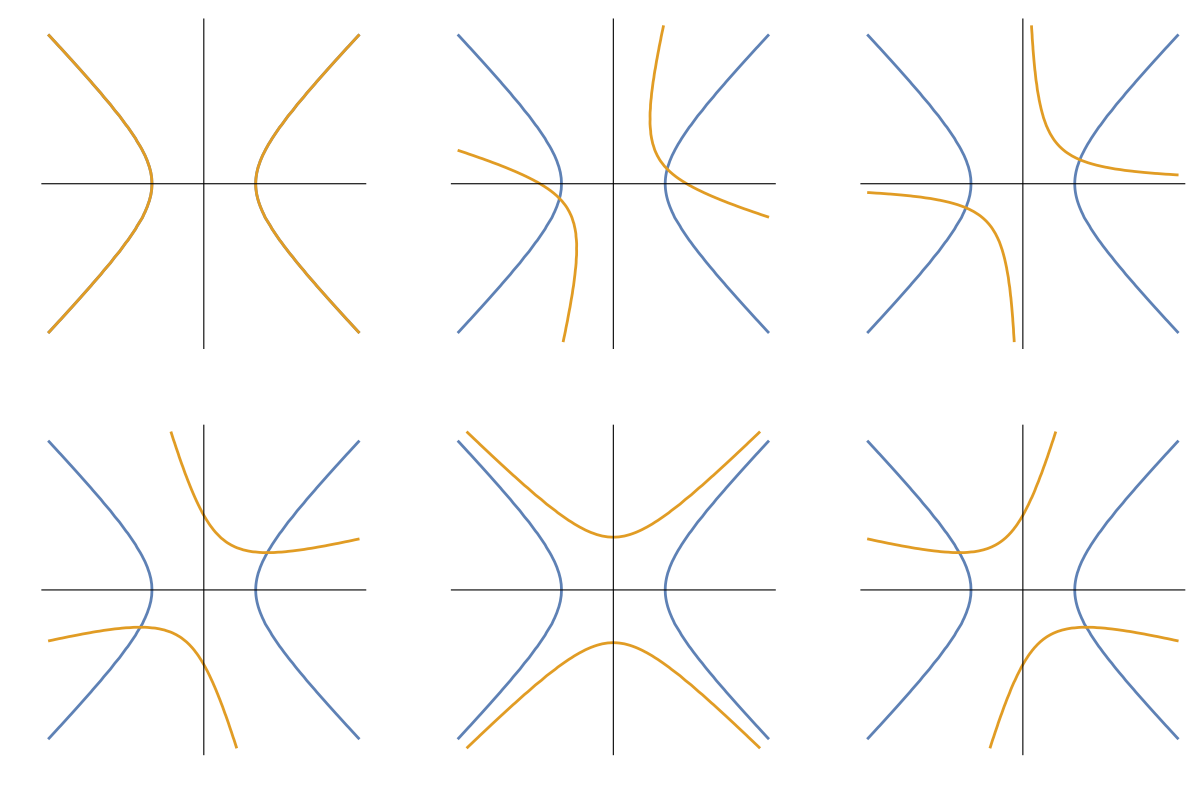

```mathematica
ContourPlot[{x1^2-x2^2==1(*单位双曲线*),{x1,x2}.RotationMatrix[#].{{1,0},{0,-1}}(*矩阵表示二次型形状*).(Transpose@RotationMatrix[#]).{x1,x2}-1==0(*使用旋转矩阵实现旋转*)},{x1,-3,3},{x2,-3,3},PlotTheme->"Minimal"]&/@{0,Pi/6,Pi/4,Pi/3,Pi/2,2Pi/3}//ArrayReshape[#,{2,3}]&//GraphicsGrid
```

圆锥曲线切线

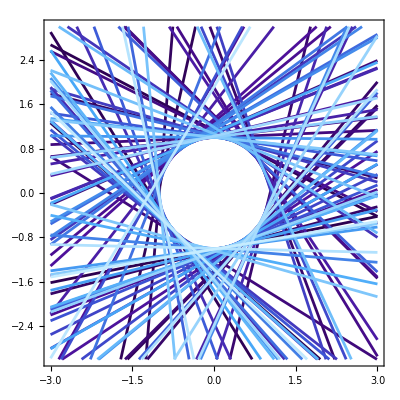
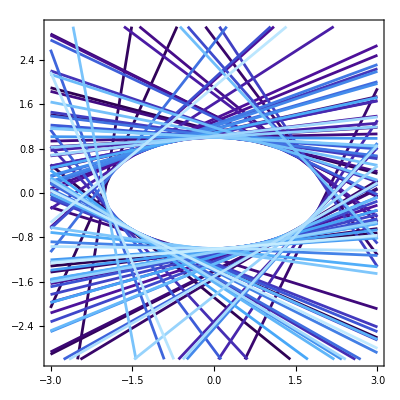
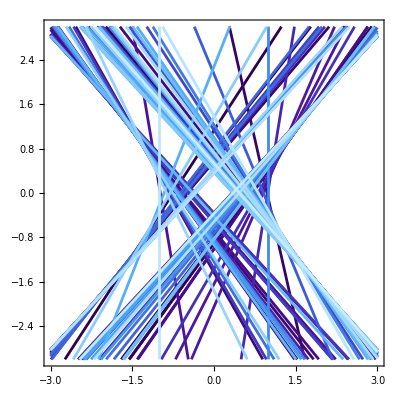

```mathematica
Show[ContourPlot[#[[1]],{p1,-3,3},{p2,-3,3}],ContourPlot[Evaluate[#[[2]]/.FindInstance[{#[[1]],-3<=p1<=3,-3<=p2<=3},{p1,p2},Reals,100](*在圆锥曲线上取点*)],{x1,-3,3},{x2,-3,3},ContourStyle->ResourceFunction["SampleColors"]["DeepSeaColors",100](*调节绘制颜色*)]]&/@{{p1^2+p2^2==1,p1 x1+p2 x2==1},{p1^2/4+p2^2==1,p1 x1/4+p2 x2==1},{p1^2-p2^2==1,p1 x1-p2 x2==1}}(*圆锥曲线方程和切线方程*)
```

二次曲面

```mathematica
plotQuadratic[a_,b_,c_]:=#[a x1^2+2 b x1 x2+c x2^2,Element[{x1,x2},Disk[{0,0},2]],PlotTheme->"Minimal",ColorFunction->"Rainbow"]&/@{Plot3D,ContourPlot}
```

```mathematica
Manipulate[plotQuadratic[a,b,c],{a,-2,2},{b,-2,2},{c,-2,2}]
```

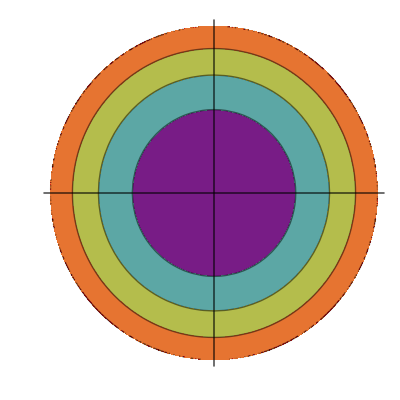
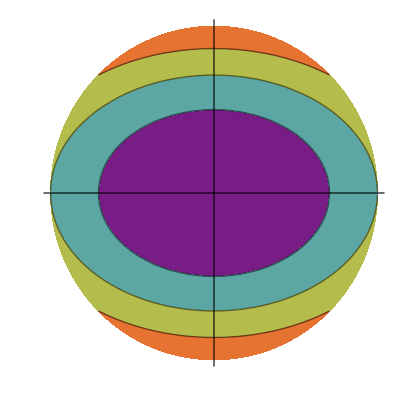
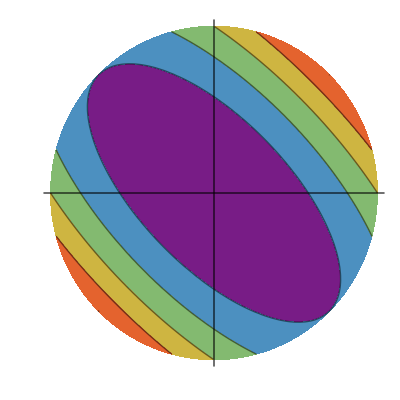
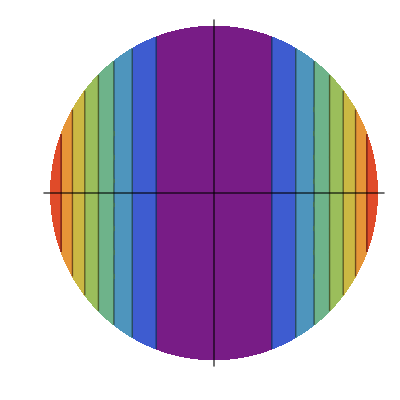
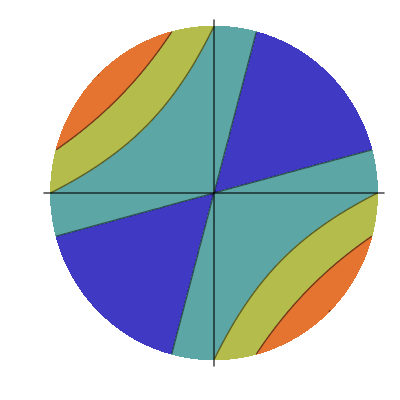
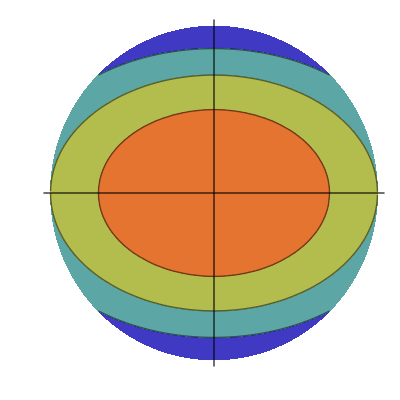
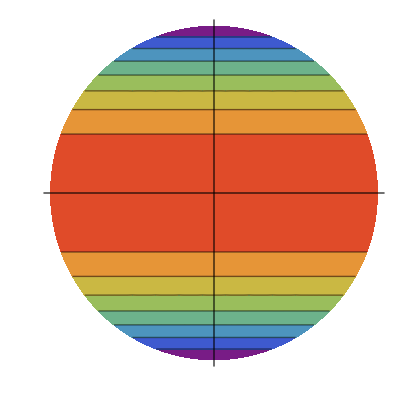
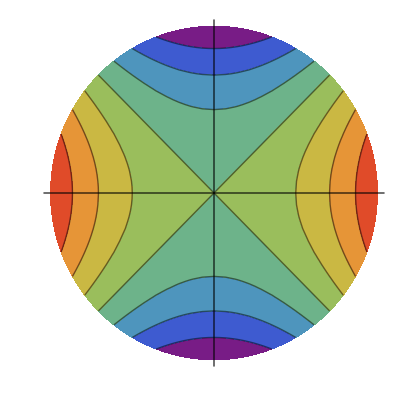
{{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-}}

```mathematica
plotQuadratic[#[[1,1]],#[[1,2]]+#[[2,1]],#[[2,2]]]&/@{{{1,0},{0,1}}(*正圆*),{{1,0},{0,2}}(*正椭圆*),{{1.5,0.5},{0.5,1.5}}(*旋转椭圆*),{{1,0},{0,0}}(*山谷面*),{{0.5,-0.5},{-0.5,0.5}}(*旋转山谷面*),{{-1,0},{0,-2}}(*开口朝下抛物面*),{{0,0},{0,-1}}(*山脊面*),{{1,0},{0,-1}}(*双曲抛物面*),{{0,-1},{-1,0}}(*旋转双曲抛物面*)}
```

多极值曲面

```mathematica
complexFunction[x1_,x2_]=3(1-x1)^2Exp[-x1^2-(x2+1)^2]-10(x1/5-x1^3-x2^5)Exp[-x1^2-x2^2]-1/3 Exp[-(x1+1)^2-x2^2];
{dx1,dx2,dx11,dx22}=D[complexFunction[x,y],#]&/@{x,y,{x,2},{y,2}};(*求各种偏导*)
dx12=D[dx1,y];
```

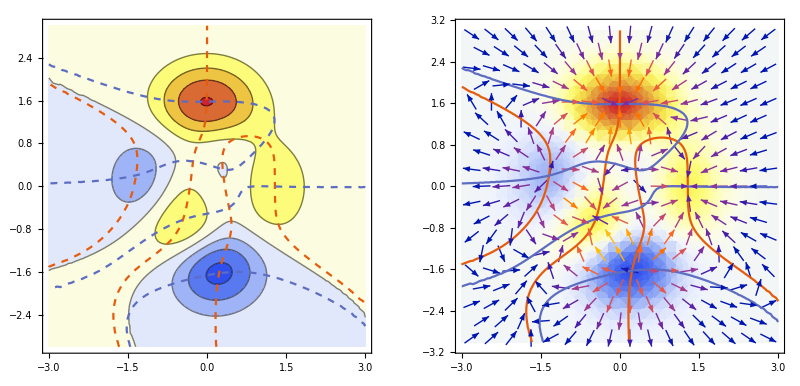

```mathematica
{Show[ContourPlot[complexFunction[x,y],{x,-3,3},{y,-3,3},ColorFunction->"TemperatureMap",PlotRange->All],ContourPlot[{dx1==0,dx2==0},{x,-3,3},{y,-3,3},ContourStyle->Dashed,PlotTheme->"Scientific"]],(*曲线交点为极值点或鞍点*)
Show[DensityPlot[complexFunction[x,y],{x,-3,3},{y,-3,3},ColorFunction->"TemperatureMap",PlotRange->All],VectorPlot[Evaluate@Grad[complexFunction[x,y],{x,y}],{x,-3,3},{y,-3,3},PlotRange->All],ContourPlot[{dx1==0,dx2==0},{x,-3,3},{y,-3,3},PlotTheme->"Scientific"]]}//GraphicsRow
```

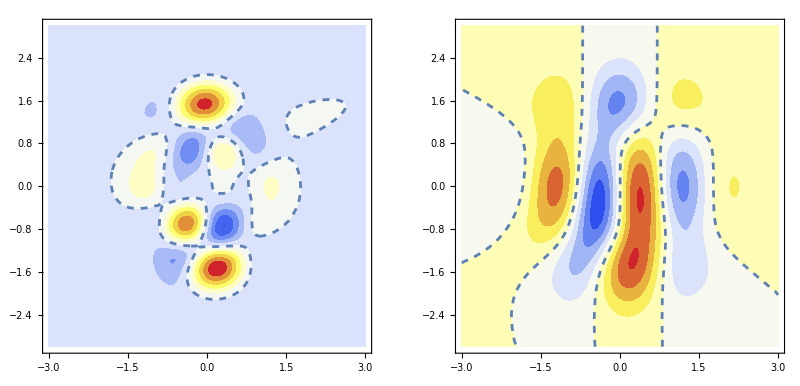

```mathematica
{Show[ContourPlot[dx11 dx22-dx12^2,{x,-3,3},{y,-3,3},ColorFunction->"TemperatureMap",ContourStyle->None,PlotRange->All],ContourPlot[dx11 dx22-dx12^2==0,{x,-3,3},{y,-3,3},ContourStyle->Dashed]](*黑塞矩阵行列式*),Show[ContourPlot[dx11,{x,-3,3},{y,-3,3},ColorFunction->"TemperatureMap",ContourStyle->None,PlotRange->All],ContourPlot[dx11==0,{x,-3,3},{y,-3,3},ContourStyle->Dashed]](*一阶主子式*)}//GraphicsRow
```